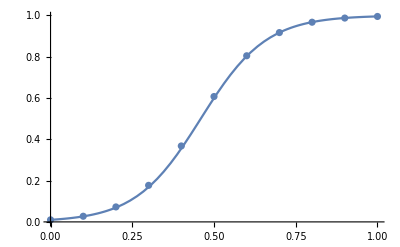

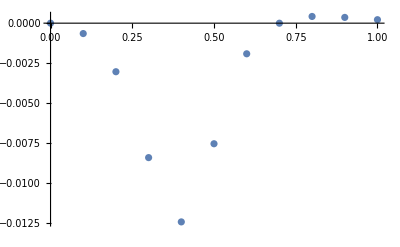

```mathematica
RK4[f_,t0_,T_,u0_,h_]:=(
p1=1/3;
p2=1/6;
p3=1/6;
p4=1/3;
n=Ceiling[(T-t0)/h];
tc=t0;
uc=u0;
res=Table[0,n+1];
res[[1]]=u0;
For[k=1,k≤n,k++,
k1=h*f[tc,uc];
k2=h*f[tc+1/2*h,uc+1/2*k1];
k3=h*f[tc+1/2*h,uc+1/2*k2];
k4=h*f[tc+h,uc+k3];
res[[k+1]]=res[[k]]+p1*k1+p2*k2+p3*k3+p4*k4;
tc=tc+h;
uc=res[[k+1]];
];
res)
f[t_,u_]:=10*u*(1-u);
ur[t_]:=0.01/(0.01+0.99*Exp[-10*t]);
T=1;
t0=0;
u0=0.01;
For[k=1,k≤4,k++,
h=10^(-k);
n=Ceiling[(T-t0)/h];
x=Table[t0+k*h,{k,0,n}];
y=RK4[f,t0,T,u0,h];
approxSol=ListPlot[Table[{x[[k]],y[[k]]},{k,1,n+1}]];
realSol=Plot[ur[t],{t,t0,T}];
Print[Show[approxSol,realSol]];Print[ListPlot[Table[{x[[k]],ur[(k-1)*h]-y[[k]]},{k,1,n+1}]]];
]
```